```mathematica
detector={R->350,L->500,h->18}
```

{R→350,L→500,h→18}

```mathematica
R/.detector
```

```mathematica
drawDetector[d_]:=Block[{R,L,h},
{{FaceForm[],EdgeForm[Thin],Rectangle[{-L/2,-R-h/2},{L/2,-R+h/2}],
Rectangle[{-L/2,R-h/2},{L/2,R+h/2}]
}
}/.d]
```

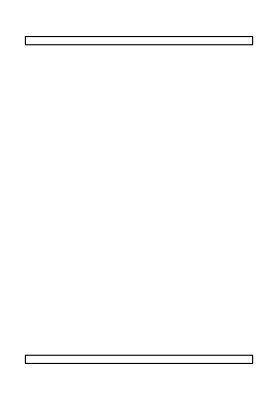

```mathematica
drawDetector[detector]//Graphics
```

```mathematica
drawEvent[e_,d_]:=Block[{x,y,ϕ,R,h,xu,xd},
x=e[[1,1]];
y=e[[1,2]];
ϕ=e[[2]];
xu= x+ (R-h/2-y)Tan[ϕ]/.d;
xd= x- (R-h/2+y)Tan[ϕ]/.d;
{PointSize[0.02],Point[{x,y}],Line[{{xd,-R+h/2},{xu,R-h/2}}]}/.d]
```

```mathematica
event1= {{0,0},20 Degree}
```

{{0,0},20 °}

```mathematica
event2= {{-100,200},-30 Degree}
```

{{-100,200},-30 °}

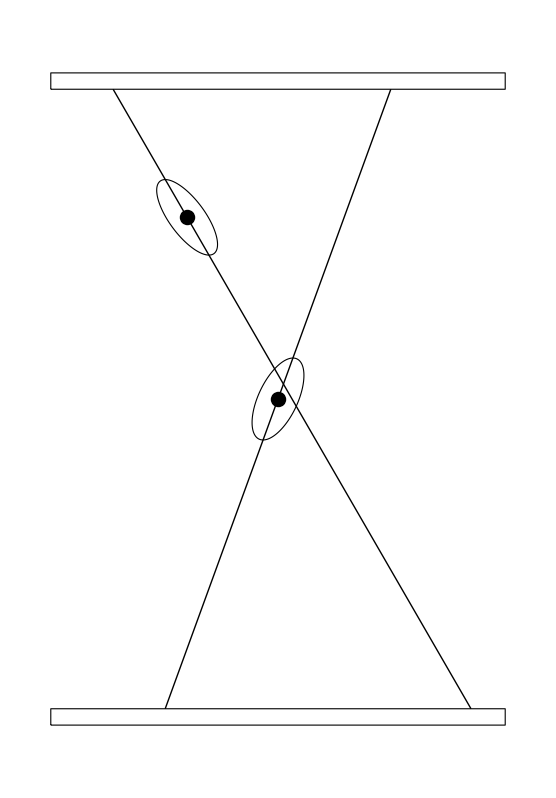

```mathematica
{drawDetector[detector],drawEvent[event1,detector],tolEllipse[event1,11,32,3],drawEvent[event2,detector],tolEllipse[event2,11,32,3]}//Graphics
```

```mathematica
pixelgrid={ll->{-250,-250},ur->{250,250},nx->100,ny->100}
```

{ll→{-250,-250},ur→{250,250},nx→100,ny→100}

```mathematica
drawPixelGrid[pg_]:=Block[{ll,ur,nx,ny,x,y,dx,dy},
ll=ll/.pg;
ur=ur/.pg;
nx=nx/.pg;
ny=ny/.pg;
dx=((ur[[1]]-ll[[1]])/nx);
dy=((ur[[2]]-ll[[2]])/ny);

{
Table[
Line[{
{x dx +ll[[1]],ll[[2]]},
{x dx +ll[[1]],ur[[2]]}}
],{x,0,nx}],

Table[
Line[{
{ll[[1]],y dy+ll[[2]]},
{ur[[1]],y dy +ll[[2]]}}
],{y,0,ny}]
}



]
```

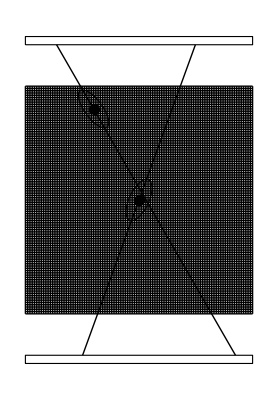

```mathematica
{drawDetector[detector],drawPixelGrid[pixelgrid],drawEvent[event1,detector],tolEllipse[event1,11,32,3],drawEvent[event2,detector],tolEllipse[event2,11,32,3]}//Graphics
```

```mathematica
3*tol[11,32,0]
```

{23.3345,48.}

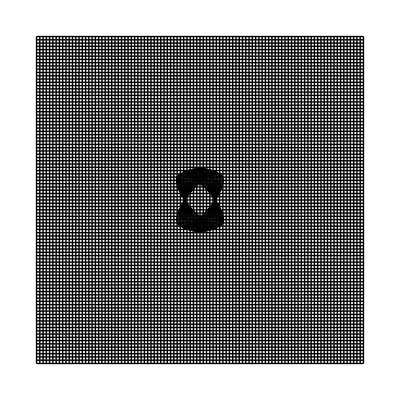

```mathematica
{drawPixelGrid[pixelgrid],Table[tolEllipse[{{0,0},ϕ},11,32,3],{ϕ,-35 Degree,35 Degree,3 Degree}]}//Graphics
```